```mathematica
Homework 2
```

```mathematica
Knowles,John
```

```mathematica
{{FullForm, Plus, Times, List, Head, Apply(@@)}, {TreeForm, Rational, Power, Factorial, Floor, Ceiling}, {Inner, Thread, Min, Max, Outer, TableForm}}
```

```mathematica
1. Problem 4.1
```

```mathematica
cs[n_]:=Plus@@(Range[n]^3)
```

```mathematica
ep[n_]:=1+Plus@@(1/Range[n]!)
```

```mathematica
ps[n_]:=Times@@(1+x^Range[n])
```

```mathematica
SetAttributes[cs,SequenceHold]
```

```mathematica
cs[3]
```

36

```mathematica
ep[3]
```

8/3

```mathematica
ps[3]
```

(1+x) (1+x^2) (1+x^3)

```mathematica
2. Problem 4.2
```

```mathematica
Select[Range[1000],Apply[Plus,Range[3,#+2]^#]==(#+3)^#&]
```

{2,3}

```mathematica
3. Exercise 4.1
```

```mathematica
Select[Range[10,99],Divisible[#,Plus@@IntegerDigits[#]]&]
```

{10,12,18,20,21,24,27,30,36,40,42,45,48,50,54,60,63,70,72,80,81,84,90}

```mathematica
Length[Select[Range[10000,99999],Divisible[#,Plus@@IntegerDigits[#]]&]]
```

10334

```mathematica
4. Problem 4.3
```

```mathematica
FactorInteger[42]
```

{{2,1},{3,1},{7,1}}

```mathematica
Last /@ FactorInteger[42]
```

{1,1,1}

```mathematica
Times@@Last/@FactorInteger[42]
```

1

```mathematica
squareFree1Q[n_]:=(Times@@Last/@FactorInteger[n])==1
```

```mathematica
squareFree1Q/@{12,13,234,1015,42}
```

{False,True,False,True,True}

```mathematica
5. Problem 4.4
```

```mathematica
Factorial/@IntegerDigits[145]
```

{1,24,120}

```mathematica
Plus@@%
```

145

```mathematica
Select[Range[1000000],Plus@@Factorial/@IntegerDigits[#]==#&]
```

{1,2,145,40585}

```mathematica
6. Problem 4.5
```

```mathematica
Divisors[6]
```

{1,2,3,6}

```mathematica
Most[Divisors[6]]
```

{1,2,3}

```mathematica
Plus@@Most[Divisors[6]]
```

6

```mathematica
Apply[Plus,Most[Divisors[6]]]
```

6

```mathematica
Select[Range[10000],#==Apply[Plus,Most[Divisors[#]]]&]
```

{6,28,496,8128}

```mathematica
7. Problem 4.6
```

```mathematica
?Floor
```

Floor[x] gives the greatest integer less than or equal to x. 
Floor[x,a] gives the greatest multiple of a less than or equal to x.

```mathematica
?Mod
```

Mod[m,n] gives the remainder on division of m by n. 
Mod[m,n,d] uses an offset d.

```mathematica
N[Sqrt[100000]]
```

316.228

```mathematica
Range[Floor[Sqrt[100000]]];
```

```mathematica
Select[Range[100000],(Mod[#,LCM@@Range[Floor[Sqrt[#]]]]==0)&]
```

{1,2,3,4,6,8,12,24}

```mathematica
8. Exercise 4.2
```

```mathematica
1/x^Range[5]
```

{1/x,1/x^2,1/x^3,1/x^4,1/x^5}

```mathematica
?Inner
```

Inner[f,list_1,list_2,g] is a generalization of Dot in which f plays the role of multiplication and g of addition.

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,{1}] or f@@@expr replaces heads at level 1 of expr by f.
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec. 
Apply[f] represents an operator form of Apply that can be applied to an expression.

```mathematica
?Thread
```

Thread[f[args]] "threads" f over any lists that appear in args. 
Thread[f[args],h] threads f over any objects with head h that appear in args. 
Thread[f[args],h,n] threads f over objects with head h that appear in the first n args.

```mathematica
Thread[List[x^Range[5],1/x^Range[5]]]
```

{{x,1/x},{x^2,1/x^2},{x^3,1/x^3},{x^4,1/x^4},{x^5,1/x^5}}

```mathematica
Inner[List,x^Range[5],1/x^Range[5],List]
```

{{x,1/x},{x^2,1/x^2},{x^3,1/x^3},{x^4,1/x^4},{x^5,1/x^5}}

```mathematica
Times@@Apply[Plus,%,1]
```

(1/x+x) (1/x^2+x^2) (1/x^3+x^3) (1/x^4+x^4) (1/x^5+x^5)

```mathematica
g[n_]:=Times@@Apply[Plus,Inner[List,x^Range[n],1/x^Range[n],List],1]
```

```mathematica
t[n_]:=Times@@Apply[Plus,Thread[List[x^Range[n],1/x^Range[n]]],1]
```

```mathematica
g[5]
```

(1/x+x) (1/x^2+x^2) (1/x^3+x^3) (1/x^4+x^4) (1/x^5+x^5)

```mathematica
t[5]
```

(1/x+x) (1/x^2+x^2) (1/x^3+x^3) (1/x^4+x^4) (1/x^5+x^5)

```mathematica
(*Both Do the same thing using different functions.*)
```

```mathematica
9. Exercise 4.3
```

```mathematica
?First
```

First[expr] gives the first element in expr. 
First[expr,def] gives the first element if it exists, or def otherwise.

```mathematica
FactorInteger[2^4*5^3*7^3]
```

{{2,4},{5,3},{7,3}}

```mathematica
FactorInteger[2520]
```

{{2,3},{3,2},{5,1},{7,1}}

```mathematica
Times@@@FactorInteger[2520]
```

{6,6,5,7}

```mathematica
Select[Range[100],(Apply[Plus,Times@@@FactorInteger[#]]==#)&]
```

{1,2,3,4,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
10. Exercise 4.4
```

```mathematica
f[n_]:=3 n^2+n+1
sd[n_]:=Plus@@IntegerDigits[n]
```

```mathematica
Min[sd/@(f/@Range[9999])]
```

3

```mathematica
11. Exercise 4.5
```

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

```mathematica
Power@@(x+y)
```

x^y

```mathematica
TreeForm[Power@@(x+y)];
```

```mathematica
TreeForm[Plus@@(x^y+y^z)];
```

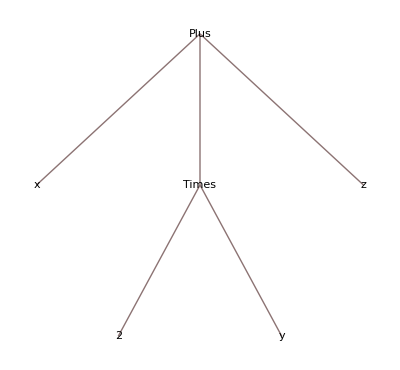

```mathematica
TreeForm[Plus@@@(x^y+y^z)]
```

```mathematica
Plus@@@(x^y+y^z)
```

x+2 y+z

```mathematica
(*Power @@ applies y as the exponent order of x, or rather, changes the head of the expression. Plus @@@ Changes the head of the expression at level 1. The effect is then the summation of all terms. *)
```

```mathematica
12. Exercise 4.6
```

```mathematica
t=Divisors[6086555670238378989670371734243169622657830773351885970528324860512791691264];
```

```mathematica
Length[t]
```

8128

```mathematica
t1=Plus@@t
```

14474011154664524427946373126085988481573677491474835889066354349131199152128

```mathematica
Apply[Plus,Most[Divisors[t1]]]==t1
```

True

```mathematica
13. Exercise 4.7
```

```mathematica
Most[Divisors[100]]>100
```

{1,2,4,5,10,20,25,50}>100

```mathematica
Select[Range[100],(((Plus@@Most[Divisors[#]])>#) &&(Times@@(DeleteDuplicates[Plus @@@ Subsets[Most[Divisors[#]]]]-#))≠0)&]
```

{70}

```mathematica
?Subsets
```

RowBox[{"Subsets", "[", StyleBox["list", "TI"], "]"}] gives a list of all possible subsets of StyleBox["list", "TI"]. 
RowBox[{"Subsets", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives all subsets containing at most StyleBox["n", "TI"] elements. 
RowBox[{"Subsets", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", StyleBox["n", "TI"], "}"}]}], "]"}] gives all subsets containing exactly StyleBox["n", "TI"] elements. 
RowBox[{"Subsets", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] gives all subsets containing between SubscriptBox[StyleBox["n", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["n", "TI"], StyleBox["max", "TI"]] elements. 
RowBox[{"Subsets", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["nspec", "TI"], ",", StyleBox["s", "TI"]}], "]"}] limits the result to the first StyleBox["s", "TI"] subsets. 
RowBox[{"Subsets", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["nspec", "TI"], ",", RowBox[{"{", StyleBox["s", "TI"], "}"}]}], "]"}] gives if possible the StyleBox[RowBox[{StyleBox["s", "TI"], ""}]]SuperscriptBox["", "th"] subset.

```mathematica
?DeleteDuplicates
```

DeleteDuplicates[list] deletes all duplicates from list.
DeleteDuplicates[list,test] applies test to pairs of elements to determine whether they should be considered duplicates.

```mathematica
14. Exercise 1
```

```mathematica
Total[#&[Range[2015]]]
```

2031120

```mathematica
15. Exercise 2
```

```mathematica
Function[n,Sum[i,{i,1,n}]]/@Range[50]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275}

```mathematica
16. Exercise 3
```

```mathematica
Count[Function[n,IntegerQ[Sum[i,{i,1,n}]/7]]/@Range[100],True]
```

28

```mathematica
Function[n,Sum[i,{i,1,n}]]/@Range[100]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275,1326,1378,1431,1485,1540,1596,1653,1711,1770,1830,1891,1953,2016,2080,2145,2211,2278,2346,2415,2485,2556,2628,2701,2775,2850,2926,3003,3081,3160,3240,3321,3403,3486,3570,3655,3741,3828,3916,4005,4095,4186,4278,4371,4465,4560,4656,4753,4851,4950,5050}

```mathematica
IntegerQ /@ (Function[n,Sum[i,{i,1,n}]]/@Range[100])
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Map[Count[Function[n,IntegerQ[Sum[i,{i,1,n}]/#]]/@Range[100],True]&,Range[100]]
```

{100,50,66,24,40,33,28,12,22,20,18,16,14,13,26,6,10,10,10,9,18,9,8,8,8,6,6,5,6,13,6,2,12,5,10,5,4,5,9,5,4,8,4,4,9,4,4,4,4,4,6,2,2,2,6,2,6,2,2,5,2,2,6,0,5,5,2,1,5,4,2,2,2,1,5,2,5,3,2,2,2,1,2,3,4,1,4,1,2,4,4,1,4,1,4,1,2,1,4,1}

```mathematica
?Inner
```

Inner[f,list_1,list_2,g] is a generalization of Dot in which f plays the role of multiplication and g of addition.

```mathematica
17. Exercise 4
```

```mathematica
Total[Range[100]//#^2&]
```

338350

```mathematica
18. Exercise 5
```

```mathematica
Total[Range[50]//#^3&]
```

1625625

```mathematica
19. Exercise 6
```

```mathematica
f[n_]:=Sum[i^3,{i,1,n}]== Sum[i,{i,1,n}]^2
```

```mathematica
f/@Range[100]
```

0

```mathematica
f[n_]:=Sum[i^4,{i,1,n}]== Sum[i,{i,1,n}]^3
```

```mathematica
f/@Range[100]
```

{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
f[n_]:=Sum[i^3,{i,1,n}]== (n^2(n+1)^2)/4
```

```mathematica
f/@Range[100]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
f[n_]:=Sum[i^5,{i,1,n}]== (n^3(n+1)^3)/6
```

```mathematica
f/@Range[100]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
20. Exercise 7
```

```mathematica
f[n_]:=Sum[i^(2n),{i,1,n}]
```

```mathematica
h=Function[{n,k},Sum[i^(k),{i,1,n}]][Range[10],Range[10]]
```

{{1,3,6,10,15,21,28,36,45,55},{1,5,14,30,55,91,140,204,285,385},{1,9,36,100,225,441,784,1296,2025,3025},{1,17,98,354,979,2275,4676,8772,15333,25333},{1,33,276,1300,4425,12201,29008,61776,120825,220825},{1,65,794,4890,20515,67171,184820,446964,978405,1978405},{1,129,2316,18700,96825,376761,1200304,3297456,8080425,18080425},{1,257,6818,72354,462979,2142595,7907396,24684612,67731333,167731333},{1,513,20196,282340,2235465,12313161,52666768,186884496,574304985,1574304985},{1,1025,60074,1108650,10874275,71340451,353815700,1427557524,4914341925,14914341925}}

```mathematica
f[Range[10]]
```

{{1,5,14,30,55,91,140,204,285,385},{1,17,98,354,979,2275,4676,8772,15333,25333},{1,65,794,4890,20515,67171,184820,446964,978405,1978405},{1,257,6818,72354,462979,2142595,7907396,24684612,67731333,167731333},{1,1025,60074,1108650,10874275,71340451,353815700,1427557524,4914341925,14914341925},{1,4097,535538,17312754,261453379,2438235715,16279522916,84998999652,367428536133,1367428536133},{1,16385,4799354,273234810,6376750435,84740914531,762963987380,5161010498484,28037802953445,128037802953445},{1,65537,43112258,4338079554,156925970179,2978035877635,36210966447236,317685943157892,2170706132009733,12170706132009733},{1,262145,387682634,69107159370,3883804424995,105443761093411,1733857359003860,19748255868485844,169842891165484965,1169842891165484965},{1,1048577,3487832978,1102999460754,96470431101379,3752628871164355,83544895168776356,1236466399775623332,13394131858832552133,113394131858832552133}}

```mathematica
Inner[List,f[Range[10]],h,LCM]
```

{{{19399380,1},{19399380,14126278634325},{19399380,520626811152185892},{19399380,1193986838382924300},{19399380,196263061458397473622180725},{19399380,396056705994140255442152775},{19399380,16430226486170123931438631019600},{19399380,229201072585449219691113774096},{19399380,4971082867319173308568942067165475},{19399380,69227145191798591455669151859743825}},{{323692753889719113900,1},{323692753889719113900,14126278634325},{323692753889719113900,520626811152185892},{323692753889719113900,1193986838382924300},{323692753889719113900,196263061458397473622180725},{323692753889719113900,396056705994140255442152775},{323692753889719113900,16430226486170123931438631019600},{323692753889719113900,229201072585449219691113774096},{323692753889719113900,4971082867319173308568942067165475},{323692753889719113900,69227145191798591455669151859743825}},{{66475180473706973307866233646940,1},{66475180473706973307866233646940,14126278634325},{66475180473706973307866233646940,520626811152185892},{66475180473706973307866233646940,1193986838382924300},{66475180473706973307866233646940,196263061458397473622180725},{66475180473706973307866233646940,396056705994140255442152775},{66475180473706973307866233646940,16430226486170123931438631019600},{66475180473706973307866233646940,229201072585449219691113774096},{66475180473706973307866233646940,4971082867319173308568942067165475},{66475180473706973307866233646940,69227145191798591455669151859743825}},{{1776112703849382134514282911333016109318218420,1},{1776112703849382134514282911333016109318218420,14126278634325},{1776112703849382134514282911333016109318218420,520626811152185892},{1776112703849382134514282911333016109318218420,1193986838382924300},{1776112703849382134514282911333016109318218420,196263061458397473622180725},{1776112703849382134514282911333016109318218420,396056705994140255442152775},{1776112703849382134514282911333016109318218420,16430226486170123931438631019600},{1776112703849382134514282911333016109318218420,229201072585449219691113774096},{1776112703849382134514282911333016109318218420,4971082867319173308568942067165475},{1776112703849382134514282911333016109318218420,69227145191798591455669151859743825}},{{745399451760125522661043874644069583308073022804300,1},{745399451760125522661043874644069583308073022804300,14126278634325},{745399451760125522661043874644069583308073022804300,520626811152185892},{745399451760125522661043874644069583308073022804300,1193986838382924300},{745399451760125522661043874644069583308073022804300,196263061458397473622180725},{745399451760125522661043874644069583308073022804300,396056705994140255442152775},{745399451760125522661043874644069583308073022804300,16430226486170123931438631019600},{745399451760125522661043874644069583308073022804300,229201072585449219691113774096},{745399451760125522661043874644069583308073022804300,4971082867319173308568942067165475},{745399451760125522661043874644069583308073022804300,69227145191798591455669151859743825}},{{625203315490492949969974134993616389736390339803975704454545917811079032940,1},{625203315490492949969974134993616389736390339803975704454545917811079032940,14126278634325},{625203315490492949969974134993616389736390339803975704454545917811079032940,520626811152185892},{625203315490492949969974134993616389736390339803975704454545917811079032940,1193986838382924300},{625203315490492949969974134993616389736390339803975704454545917811079032940,196263061458397473622180725},{625203315490492949969974134993616389736390339803975704454545917811079032940,396056705994140255442152775},{625203315490492949969974134993616389736390339803975704454545917811079032940,16430226486170123931438631019600},{625203315490492949969974134993616389736390339803975704454545917811079032940,229201072585449219691113774096},{625203315490492949969974134993616389736390339803975704454545917811079032940,4971082867319173308568942067165475},{625203315490492949969974134993616389736390339803975704454545917811079032940,69227145191798591455669151859743825}},{{9718234233266837990148983403462509024952388043083808458120586458151363567670060,1},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,14126278634325},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,520626811152185892},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,1193986838382924300},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,196263061458397473622180725},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,396056705994140255442152775},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,16430226486170123931438631019600},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,229201072585449219691113774096},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,4971082867319173308568942067165475},{9718234233266837990148983403462509024952388043083808458120586458151363567670060,69227145191798591455669151859743825}},{{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,1},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,14126278634325},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,520626811152185892},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,1193986838382924300},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,196263061458397473622180725},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,396056705994140255442152775},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,16430226486170123931438631019600},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,229201072585449219691113774096},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,4971082867319173308568942067165475},{19901661615686109821751713767005734273890933890307268237951201320883759346719808642025276917385140,69227145191798591455669151859743825}},{{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,1},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,14126278634325},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,520626811152185892},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,1193986838382924300},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,196263061458397473622180725},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,396056705994140255442152775},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,16430226486170123931438631019600},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,229201072585449219691113774096},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,4971082867319173308568942067165475},{416732168703617445340566254222071756419108478306593382525107266253839020263986531699663494502075730360540,69227145191798591455669151859743825}},{{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,1},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,14126278634325},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,520626811152185892},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,1193986838382924300},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,196263061458397473622180725},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,396056705994140255442152775},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,16430226486170123931438631019600},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,229201072585449219691113774096},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,4971082867319173308568942067165475},{1991784871675419339007206070652228363578389702472968547312686759104188781597843188757146869793824629137009437832662406218780,69227145191798591455669151859743825}}}

```mathematica
21. Exercise 8
```

```mathematica
Outer[Function[{n,k},Sum[i^k,{i,1,n}]],Range[5],Range[5]]//TableForm
```

1 | 1 | 1 | 1 | 1
3 | 5 | 9 | 17 | 33
6 | 14 | 36 | 98 | 276
10 | 30 | 100 | 354 | 1300
15 | 55 | 225 | 979 | 4425

```mathematica
(*This function generates all possibile values for different n, k, and the sum of this value and the previous iteration, or graphically, the previous row, is the total listed in the matrix*)
```

```mathematica
Outer[Function[{n,k},Map[Sum[i^k/#,{i,1,n}]&,Range[10]]],Range[10],Range[10]];
```

```mathematica
Outer[Function[{n,k},Length[Select[Map[Sum[i^k/#,{i,1,n}]&,Range[10]],IntegerQ]]],Range[10],Range[10]]
```

{{1,1,1,1,1,1,1,1,1,1},{2,2,3,1,2,2,2,1,3,2},{4,3,6,3,5,2,5,3,6,3},{4,6,5,4,5,6,5,4,5,6},{3,2,4,1,3,2,3,1,4,2},{3,2,4,3,3,1,3,3,4,2},{4,6,5,4,5,5,5,4,5,6},{6,5,7,5,7,6,7,5,7,5},{4,3,4,2,4,3,4,2,4,3},{2,3,2,2,2,2,2,2,2,3}}

```mathematica
(*For each full iteration, k fully divides each iteration by the above number of times.*)
```

```mathematica
22. Exercise 9
```

```mathematica
Function[{n,k},Sum[DivisorSigma[k,n],{k,1,n}]]
```

Function[{n,k},∑_(k=1)^n DivisorSigma[k,n]]